```mathematica
Dipole dipole with brute force
```

Article the référence
Bowden et al Journ. Phys. C 14, L827 (1981)
Hayashi et al Jap. Journ. Appl. Phys. 35, 6065 (1996)
Newel et al Journ. Geo. Phys 98, 9551 (1993)

```mathematica
réseau cubique
```

```mathematica
cub={{1.0,0.0,0.0},{0.0,1.0,0.0},{0.0,0.0,1.0}};
```

```mathematica
réseau de spin de 20x20
```

```mathematica
Nx=20;
Ny=20;
Nz=1;
```

```mathematica
position=Table[(i-1)*cub[[1]]+(j-1)*cub[[2]]+(k-1)*cub[[3]],{i,1,Nx},{j,1,Ny},{k,1,Nz}];
```

```mathematica
1 Dimensional case
```

```mathematica
Sum[1/n^3,{n,1,Infinity}]
```

Zeta[3]

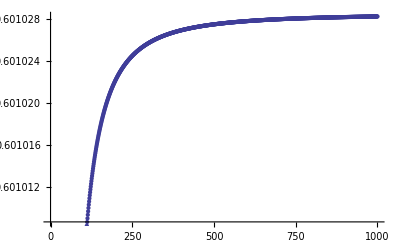

```mathematica
Convergence=Table[
Sum[
N[1.0/Abs[i]^3/2.0],{i,1,P}]
,{P,1,1000}];
ListPlot[Convergence]
```

```mathematica
demagnetization matrix (it has a super bad form. check p172 of the notebook)
```

```mathematica
F[P_,Q_]:=(
demag=Table[{0,0,0,0,0,0},{2P}];
Do[
demag[[j]]=demag[[j]]+{i^2-i^2/3.0,-i^2/3.0,-i^2/3.0,0,0,0}*1.0/i^5,{j,1,2P},{i,1,Q}];
CompDemagM=Table[{0,0,0,0,0,0},{2P}];
Do[
CompDemagM[[All,i]]=Fourier[demag[[All,i]]];,{i,1,6}];
toto=Table[{0.0,0.0,1.0},{P}];
Spin=N[ArrayPad[toto,{{0,P},{0,0}}]];
compspin=Table[{0.0,0.0,0.0},{2P}];
Do[compspin[[All,i]]=Fourier[Spin[[All,i]]];,{i,1,3}];
Hcomplex=Table[{0,0,0},{2P}];
Hreal=Table[{0,0,0},{2P}];
Do[
Hcomplex[[i,1]]=compspin[[i,1]]*CompDemagM[[i,1]]+compspin[[i,2]]*CompDemagM[[i,4]]+compspin[[i,3]]*CompDemagM[[i,6]];
Hcomplex[[i,2]]=compspin[[i,2]]*CompDemagM[[i,2]]+compspin[[i,1]]*CompDemagM[[i,4]]+compspin[[i,3]]*CompDemagM[[i,5]];
Hcomplex[[i,3]]=compspin[[i,1]]*CompDemagM[[i,6]]+compspin[[i,2]]*CompDemagM[[i,5]]+compspin[[i,3]]*CompDemagM[[i,3]];,{i,1,P}];
Do[Hreal[[All,i]]=InverseFourier[Hcomplex[[All,i]]/Sqrt[2P]];,{i,1,3}];
Return[Sum[Spin[[i]].Hreal[[i]],{i,1,P}]/P])
```

```mathematica
ListPlot3D[Table[F[j,i],{j,1,1001,100},{i,1,1001,100}]]
```

-Graphics3D-

```mathematica
MatrixForm[demag]
```

2 Dimensional case (periodic)

```mathematica
Nx=10;
Ny=10;
Spin=Table[{0.0,0.0,1.0},{Nx},{Ny}];
```

```mathematica
Edip[Nx_,Ny_]=Sum[
N[1.0/Sqrt[i^2+j^2]^3],{i,1,Nx},{j,0,Ny}];
```

```mathematica
Edip[50,50]
```

2.2304

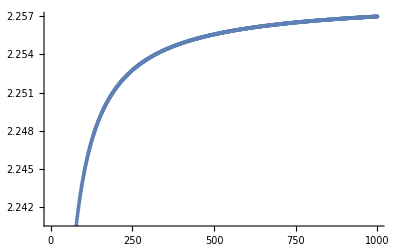

```mathematica
Convergence=Table[
Sum[
N[1.0/Sqrt[i^2+j^2]^3],{i,1,P},{j,0,P}]
,{P,1,1000}];
ListPlot[Convergence]
```

```mathematica
demagnetization matrix (it has a super bad form. check p172 of the notebook)
```

```mathematica
F[Px_,Py_,Qx_,Qy_]:=(
demag=Table[{0.0,0.0,0.0,0,0,0},{2Px},{2Py}];
Do[
Do[demag[[i,j]]=demag[[i,j]]+{(Qx+1-k)^2-((Qx+1-k)^2+(Qy-l)^2)/3.0,(Qy-l)^2-((Qx+1-k)^2+(Qy-l)^2)/3.0,-((Qx+1-k)^2+(Qy-l)^2)/3.0,(Qx+1-k)*(Qy-l),0,0}*3.0/Sqrt[(Qx+1-k)^2+(Qy-l)^2]^5;
,{k,1,Qx},{l,0,Qy}];
demag[[2Px+1-i,j]]=demag[[i,j]];
demag[[i,2Py+1-j]]=demag[[i,j]];
demag[[2Px+1-i,2Py+1-j]]=demag[[i,j]];
,{i,1,Px},{j,1,Py}];
demag[[Px+1,All]]={0.0,0.0,0.0,0,0,0};
demag[[All,Py+1]]={0.0,0.0,0.0,0,0,0};
CompDemagM=Table[{0,0,0,0,0,0},{2Px},{2Py}];
Do[
CompDemagM[[All,All,i]]=Fourier[demag[[All,All,i]]];,{i,1,6}];
toto=Table[{0.0,0.0,1.0},{Px},{Py}];
Spin=N[ArrayPad[toto,{{0,Px},{0,Py},0}]];
compspin=Table[{0.0,0.0,0.0},{2Px},{2Py}];
Do[compspin[[All,All,i]]=Fourier[Spin[[All,All,i]]];,{i,1,3}];
Hcomplex=Table[{0,0,0},{2Px},{2Py}];
Hreal=Table[{0,0,0},{2Px},{2Py}];
Do[
Hcomplex[[i,j,1]]=compspin[[i,j,1]]*CompDemagM[[i,j,1]]+compspin[[i,j,2]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,6]];
Hcomplex[[i,j,2]]=compspin[[i,j,2]]*CompDemagM[[i,j,2]]+compspin[[i,j,1]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,5]];
Hcomplex[[i,j,3]]=compspin[[i,j,1]]*CompDemagM[[i,j,6]]+compspin[[i,j,2]]*CompDemagM[[i,j,5]]+compspin[[i,j,3]]*CompDemagM[[i,j,3]];
,{i,1,Px},{j,1,Py}];
Do[Hreal[[All,All,i]]=InverseFourier[Hcomplex[[All,All,i]]/Sqrt[Px*Py]];,{i,1,3}];
Return[Sum[Spin[[i,j]].Re[Hreal[[i,j]]],{i,1,Px},{j,1,Py}]/Px/Py])
```

```mathematica
MatrixForm[demag[[All,All,4]]]
```

```mathematica
F[10,15,50,50]
```

-1.06912

```mathematica
2 Dimensional real case
```

```mathematica
Nx=50;Ny=50;
position=Table[{i-1,j-1,0.0},{i,1,Nx},{j,1,Ny}];
q={0.1,0.0,0.0};
Spin=Table[{Sin[2*Pi*q.position[[i,j]]],0.0,Cos[2*Pi*q.position[[i,j]]]},{i,1,Nx},{j,1,Ny}];
```

```mathematica
Edip[m_,n_]:=(
res=0.0;
Do[
ax=Mod[i+Nx-1,Nx]+1;
ay=Mod[j+Ny-1,Ny]+1;
r=position[[m,n]]-{i-1,j-1,0.0};
Nr=Norm[r];
If[Nr==0.0,res=res+1.0/3.0,
res=res+N[(Spin[[m,n]].Spin[[ax,ay]]*Nr^2-3.0*Spin[[m,n]].r*Spin[[ax,ay]].r)/Nr^5];],{i,-Nx+1+m,Nx+m},{j,-Ny+1+n,Ny+n}];
Return[res];);
```

```mathematica
Sum[Edip[i,j],{i,1,Nx},{j,1,Ny}]/Nx/Ny
```

2.61969

```mathematica
Edip[1,1]
```

5.80423

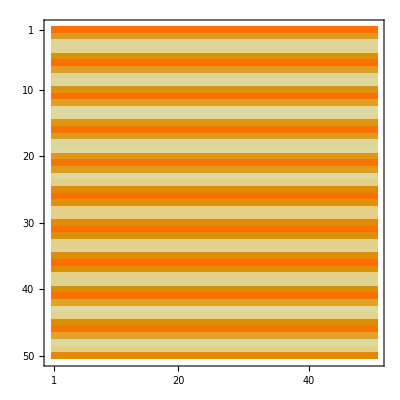

```mathematica
MatrixPlot[Table[Edip[i,j],{i,1,Nx},{j,1,Ny}]]
```

```mathematica
demag=Table[{0.0,0.0,0.0,0.0,0.0,0.0},{2Nx},{2Ny}];
Do[
Do[
ax=Mod[i+Nx-1,Nx]+1;
ay=Mod[j+Ny-1,Ny]+1;
r=position[[k,l]]-{i-1,j-1,0.0};
Nr=Norm[r];
If[Nr==0.0,demag[[k,l]]=demag[[k,l]]+{1.0,1.0,1.0,1.0,1.0,1.0}/3.0,demag[[k,l]]=demag[[k,l]]+
{r[[1]]^2-Nr^2/3.0,r[[2]]^2-Nr^2/3.0,r[[3]]^2-Nr^2/3.0,r[[1]]*r[[2]],0,0}*3.0/Nr^5;]
,{i,-Nx+1+k,Nx+k},{j,-Ny+1+l,Ny+l}];
demag[[2Nx+1-k,l]]=demag[[k,l]];
demag[[k,2Ny+1-l]]=demag[[k,l]];
demag[[2Nx+1-k,2Ny+1-l]]=demag[[k,l]];
,{k,1,Nx},{l,1,Ny}];
demag[[Nx+1,All]]={0.0,0.0,0.0,0,0,0};
demag[[All,Ny+1]]={0.0,0.0,0.0,0,0,0};
CompDemagM=Table[{0.0,0.0,0.0,0.0,0.0,0.0},{2Nx},{2Ny}];
Do[
CompDemagM[[All,All,i]]=Fourier[demag[[All,All,i]]];,{i,1,6}];
```

```mathematica
spin=ArrayPad[Spin,{{0,Nx},{0,Ny},0}];
compspin=Table[{0.0,0.0,0.0},{2Nx},{2Ny}];
Do[compspin[[All,All,i]]=Fourier[spin[[All,All,i]]];,{i,1,3}];
Hcomplex=Table[{0.0,0.0,0.0},{2Nx},{2Ny}];
Hreal=Table[{0.0,0.0,0.0},{2Nx},{2Ny}];
Do[
Hcomplex[[i,j,1]]=compspin[[i,j,1]]*CompDemagM[[i,j,1]]+compspin[[i,j,2]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,6]];
Hcomplex[[i,j,2]]=compspin[[i,j,2]]*CompDemagM[[i,j,2]]+compspin[[i,j,1]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,5]];
Hcomplex[[i,j,3]]=compspin[[i,j,1]]*CompDemagM[[i,j,6]]+compspin[[i,j,2]]*CompDemagM[[i,j,5]]+compspin[[i,j,3]]*CompDemagM[[i,j,3]];
,{i,1,2Nx},{j,1,2Ny}];
Do[Hreal[[All,All,i]]=InverseFourier[Hcomplex[[All,All,i]]];,{i,1,3}];
```

```mathematica
EFFT[m_,n_]:=Spin[[m,n]].Re[Hreal[[m+Ny,n]]]
```

```mathematica
Sum[EFFT[i,j],{i,1,Nx},{j,1,Ny}]
```

2370.98

```mathematica
EFFT[1,10]
```

0.0429357

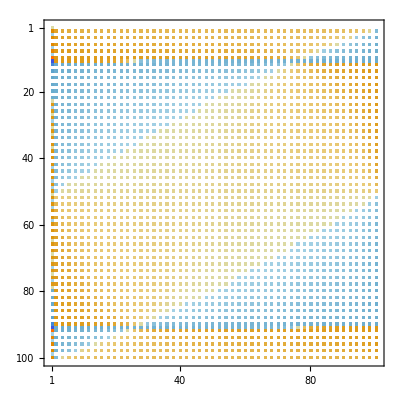

```mathematica
MatrixPlot[Hcomplex[[All,All,2]]]
```

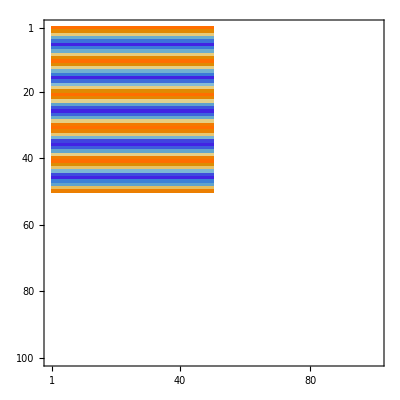

```mathematica
MatrixPlot[spin[[All,All,3]]]
```

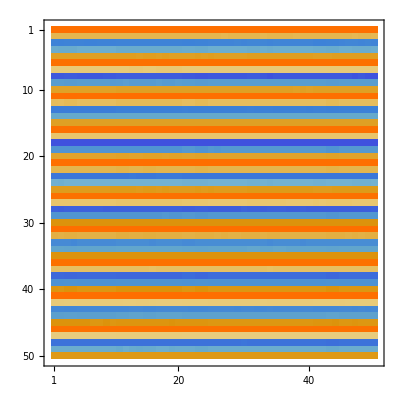

```mathematica
MatrixPlot[Table[EFFT[i,j],{i,1,Nx},{j,1,Ny}]]
```

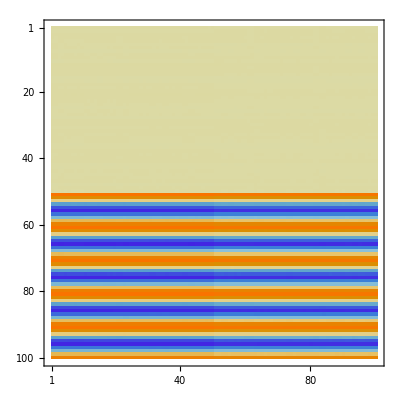

```mathematica
MatrixPlot[Hreal[[All,All,3]]]
```

```mathematica
compspin[[10,2,1]]
```

0.16646+5.29684 ⅈ

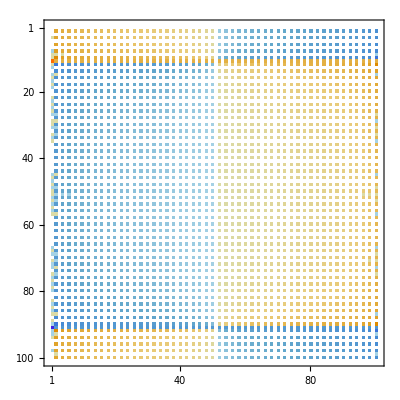

```mathematica
MatrixPlot[Im[compspin[[All,All,1]]]]
```

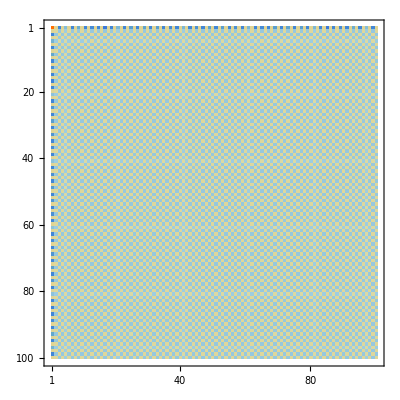

```mathematica
MatrixPlot[CompDemagM[[All,All,1]]]
```

```mathematica
MatrixForm[CompDemagM[[All,All,1]]]
```

```mathematica
on établit une matrice pour le dipole-dipole brute force
```

```mathematica
dipole dipole for out of plane magnetization
```

```mathematica
Spin=Table[{0.0,0.0,1.0},{Nx},{Ny},{Nz}];
```

```mathematica
Spin=Table[{0.0,1.0,0.0},{Nx},{Ny},{Nz}];
```

```mathematica
q={0.5,0.0,0.0};
Spin=Table[{Sin[2*Pi*q.position[[i,j,k]]],0.0,Cos[2*Pi*q.position[[i,j,k]]]},{i,1,Nx},{j,1,Ny},{k,1,Nz}];
```

```mathematica
q={0.5,0.5,0.0};
Spin=Table[{Sin[2*Pi*q.position[[i,j,k]]],Cos[2*Pi*q.position[[i,j,k]]],0.0},{i,1,Nx},{j,1,Ny},{k,1,Nz}];
```

```mathematica
Edip=0.0;
Do[
r=position[[i,j,k]]-position[[l,m,n]];
If[Norm[r]==0.0,Edip=Edip+1.0/3.0,Edip=Edip+N[(Spin[[i,j,k]].Spin[[l,m,n]]*Norm[r]^2-3.0*(r.Spin[[i,j,k]])*(r.Spin[[l,m,n]]))/Norm[r]^5]],{i,1,Nx},{j,1,Ny},{k,1,Nz},{l,1,Nx},{m,1,Ny},{n,1,Nz}]
Print[3.0*Edip/Nx/Ny/Nz/4.0/Pi]
```

1.87067

```mathematica
Analytical form and more exploration
```

```mathematica
FullSimplify[Sum[1/(i^2+j^2)^(3/2),{i,1,Nx},{j,0,Ny}]+1/3]
```

```mathematica
Edip=0.0;
Do[
r=position[[i,j,1]]-position[[k,l,1]];
If[Norm[r]==0.0,Edip=Edip+1.0/3.0,Edip=Edip+N[1.0/Norm[r]^3]],{i,1,Nx},{j,1,Ny},{k,1,Nx},{l,1,Ny}]
Print[3.0*Edip/Nx/Ny/4.0/Pi]
```

1.87067

```mathematica
For periodic lattice (all the sites will have the same contribution of ri-rj) for out of plane and inplane
```

```mathematica
Edip=0.0;
Do[
r=position[[i,j,k]];
If[Norm[r]==0.0,Edip=Edip+1.0/3.0,Edip=Edip+N[1.0/Norm[r]^3]],{i,1,Nx},{j,1,Ny},{k,1,Nz}]
Print[3.0*Edip/Pi]
```

3.55232

```mathematica
Dipole dipole with the FFT
```

```mathematica
emagnetization matrix for 0D systems
```

```mathematica
demagnetization matrix (it has a super bad form. check p172 of the notebook)
```

```mathematica
demag=Table[{0,0,0,0,0,0},{2Nx},{2Ny},{2Nz}];
Do[
r=position[[i,j,k]]-position[[l,m,n]];
If[Norm[r]==0.0,demag[[i,j,k]]=demag[[i,j,k]]+N[{1/3,1/3,1/3,1/3,1/3,1/3}],demag[[i,j,k]]=demag[[i,j,k]]+{r[[1]]^2+Norm[r]^2/3.0,r[[2]]^2+Norm[r]^2/3.0,r[[3]]^2+Norm[r]^2/3.0,r[[1]]*r[[2]],r[[3]]*r[[2]],r[[3]]*r[[1]]}*3.0/4.0/Pi/Norm[r]^5],{i,1,Nx},{j,1,Ny},{k,1,Nz},{l,1,Nx},{m,1,Ny},{n,1,Nz}]
```

```mathematica
reorganize the matrix to prepapre the FFT
```

```mathematica
demag[[Nx+2;;2Nx,1;;Ny,Nz]]=demag[[1;;Nx-1,1;;Ny,Nz]];
demag[[Nx+2;;2Nx,Ny+2;;2Ny,Nz]]=Transpose[demag[[1;;Nx-1,1;;Ny-1,Nz]]];
demag[[1;;Nx,Ny+2;;2Ny,Nz]]=demag[[1;;Nx,1;;Ny-1,Nz]];
```

```mathematica
MatrixForm[demag[[All,All,1,1]]]
```

```mathematica
Do the FFT of the matrix
```

```mathematica
CompDemagM=Table[{0,0,0,0,0,0},{2Nx},{2Ny},{2Nz}];
Do[
CompDemagM[[All,All,All,i]]=Fourier[demag[[All,All,All,i]]];,{i,1,6}]
```

```mathematica
spin matrix
```

```mathematica
MatrixForm[Spin[[All,All,1,3]]]
```

```mathematica
FFTSpin=ArrayPad[Spin,{{0,Nx},{0,Ny},{0,Nz},0}];
compspin=Table[{0,0,0,0,0,0},{2Nx},{2Ny},{2Nz}];
Do[
compspin[[All,All,All,i]]=Fourier[FFTSpin[[All,All,All,i]]];,{i,1,3}]
```

```mathematica
MatrixForm[FFTSpin[[All,All,1,3]]]
```

Calculate the depolarising field

```mathematica
Hcomplex=Table[{0,0,0},{2Nx},{2Ny},{2Nz}];
Hreal=Table[{0,0,0},{2Nx},{2Ny},{2Nz}];
Do[
Hcomplex[[i,j,k,1]]=compspin[[i,j,k,1]]*CompDemagM[[i,j,k,1]]+compspin[[i,j,k,2]]*CompDemagM[[i,j,k,4]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,6]];
Hcomplex[[i,j,k,2]]=compspin[[i,j,k,2]]*CompDemagM[[i,j,k,2]]+compspin[[i,j,k,1]]*CompDemagM[[i,j,k,4]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,5]];
Hcomplex[[i,j,k,3]]=compspin[[i,j,k,1]]*CompDemagM[[i,j,k,6]]+compspin[[i,j,k,2]]*CompDemagM[[i,j,k,5]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,3]];,{i,1,2Nx},{j,1,2Ny},{k,1,2Nz}]
Do[Hreal[[All,All,All,i]]=InverseFourier[Hcomplex[[All,All,All,i]]],{i,1,3}]
```

```mathematica
MatrixForm[Hreal[[1;;Nx,1;;Ny,1,3]]]
```

Calculation of the energy

```mathematica
Sum[Spin[[i,j,k]].Hreal[[i,j,k]],{i,1,Nx},{j,1,Ny},{k,1,Nz}]/Nx/Ny/Nz
```

6.71155

```mathematica
demagnetization matrix for periodic system
```

```mathematica
demag=Table[{0,0,0,0,0,0},{Nx},{Ny},{2Nz}];
Do[
r=position[[i,j,k]];
If[Norm[r]==0.0,demag[[i,j,k]]=demag[[i,j,k]]+N[{1/3,1/3,1/3,1/3,1/3,1/3}],demag[[i,j,k]]=demag[[i,j,k]]+{r[[1]]^2+Norm[r]^2/3.0,r[[2]]^2+Norm[r]^2/3.0,r[[3]]^2+Norm[r]^2/3.0,r[[1]]*r[[2]],r[[3]]*r[[2]],r[[3]]*r[[1]]}*3.0/Pi/4.0/Norm[r]^5],{i,1,Nx},{j,1,Ny},{k,1,Nz},{l,1,Nx},{m,1,Ny},{n,1,Nz}]
```

```mathematica
CompDemagM=Table[{0,0,0,0,0,0},{Nx},{Ny},{2Nz}];
Do[
CompDemagM[[All,All,All,i]]=Fourier[demag[[All,All,All,i]]];,{i,1,6}]
```

```mathematica
FFTSpin=ArrayPad[Spin,{0,0,{0,Nz},0}];
compspin=Table[{0,0,0,0,0,0},{Nx},{Ny},{2Nz}];
Do[
compspin[[All,All,All,i]]=Fourier[FFTSpin[[All,All,All,i]]];,{i,1,3}]
```

```mathematica
Hcomplex=Table[{0,0,0},{Nx},{Ny},{2Nz}];
Hreal=Table[{0,0,0},{Nx},{Ny},{2Nz}];
Do[
Hcomplex[[i,j,k,1]]=compspin[[i,j,k,1]]*CompDemagM[[i,j,k,1]]+compspin[[i,j,k,2]]*CompDemagM[[i,j,k,4]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,6]];
Hcomplex[[i,j,k,2]]=compspin[[i,j,k,2]]*CompDemagM[[i,j,k,2]]+compspin[[i,j,k,1]]*CompDemagM[[i,j,k,4]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,5]];
Hcomplex[[i,j,k,3]]=compspin[[i,j,k,1]]*CompDemagM[[i,j,k,6]]+compspin[[i,j,k,2]]*CompDemagM[[i,j,k,5]]+compspin[[i,j,k,3]]*CompDemagM[[i,j,k,3]];,{i,1,Nx},{j,1,Ny},{k,1,2Nz}]
Do[Hreal[[All,All,All,i]]=InverseFourier[Hcomplex[[All,All,All,i]]],{i,1,3}]
```

```mathematica
Sum[Spin[[i,j,k]].Hreal[[i,j,k]],{i,1,Nx},{j,1,Ny},{k,1,Nz}]/Nx/Ny/Nz
```

8.52536

```mathematica
réseau hexagonal
```

```mathematica
hex={{0.5,-N[Sqrt[3]/2],0.0},{0.5,N[Sqrt[3]/2],0.0},{0.0,0.0,1.0}};
```

```mathematica
position=Table[(i-1)*hex[[1]]+(j-1)*hex[[2]]+0.0*hex[[3]],{i,1,Nx},{j,1,Ny}];
```

```mathematica
dipole dipole for a spin spiral
```

```mathematica
q={0.0,0.0,0.0};
Spin=Table[{Sin[2*Pi*q.position[[i,j]]],0.0,Cos[2*Pi*q.position[[i,j]]]},{i,1,Nx},{j,1,Ny}];
Edip=0.0;
Do[
rijkl=position[[i,j]]-position[[k,l]];
If[Norm[rijkl]==0.0,Continue,Edip=Edip+N[(Spin[[i,j]].Spin[[k,l]]-3.0*(rijkl.Spin[[i,j]])*(rijkl.Spin[[k,l]]))/Norm[rijkl]^3]],{i,1,Nx},{j,1,Ny},{k,1,Nx},{l,1,Ny}]
Print[Edip/Nx/Ny]
```

9.03495

```mathematica
Dipole dipole with the FFT
```

```mathematica
demag=Table[{0,0,0,0,0,0},{2Nx},{2Ny}];
CompDemagM=Table[{0,0,0,0,0,0},{2Nx},{2Ny}];
Do[
rijkl=position[[i,j]]-position[[k,l]];
If[Norm[rijkl]==0.0,demag[[i,j]]=demag[[i,j]]+N[{1/3,1/3,1/3,1/3,1/3,1/3}],demag[[i,j]]=demag[[i,j]]+{rijkl[[1]]^2+Norm[rijkl]^2/3.0,rijkl[[2]]^2+Norm[rijkl]^2/3.0,rijkl[[3]]^2+Norm[rijkl]^2/3.0,rijkl[[1]]*rijkl[[2]],rijkl[[3]]*rijkl[[2]],rijkl[[3]]*rijkl[[1]]}*3.0/4.0/Pi/Norm[rijkl]^5],{i,1,Nx},{j,1,Ny},{k,1,Nx},{l,1,Ny}]
demag[[Nx+1;;2Nx,1;;Ny]]=demag[[1;;Nx,1;;Ny]];
demag[[Nx+1;;2Nx,Ny+1;;2Ny]]=demag[[1;;Nx,1;;Ny]];
demag[[1;;Nx,Ny+1;;2Ny]]=demag[[1;;Nx,1;;Ny]];
Do[
CompDemagM[[All,All,i]]=Fourier[demag[[All,All,i]]];,{i,1,6}]
```

```mathematica
FFTSpin=ArrayPad[Spin,{{0,Nx},{0,Ny},0}];
compspin=Table[{0,0,0,0,0,0},{2Nx},{2Ny}];
Do[
compspin[[All,All,i]]=Fourier[FFTSpin[[All,All,i]]];,{i,1,3}]
```

```mathematica
Hcomplex=Table[{0,0,0},{2Nx},{2Ny}];
Hreal=Table[{0,0,0},{2Nx},{2Ny}];
Do[
Hcomplex[[i,j,1]]=compspin[[i,j,1]]*CompDemagM[[i,j,1]]+compspin[[i,j,2]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,6]];
Hcomplex[[i,j,2]]=compspin[[i,j,2]]*CompDemagM[[i,j,2]]+compspin[[i,j,1]]*CompDemagM[[i,j,4]]+compspin[[i,j,3]]*CompDemagM[[i,j,5]];
Hcomplex[[i,j,3]]=compspin[[i,j,1]]*CompDemagM[[i,j,6]]+compspin[[i,j,2]]*CompDemagM[[i,j,5]]+compspin[[i,j,3]]*CompDemagM[[i,j,3]];,{i,1,2Nx},{j,1,2Ny}]
Do[Hreal[[All,All,i]]=InverseFourier[Hcomplex[[All,All,i]]],{i,1,3}]
```

```mathematica
Sum[Spin[[i,j]].Hreal[[i,j]],{i,1,Nx},{j,1,Ny}]/Nx/Ny
```

10.5231

```mathematica
Let' s see the real case with a lattice and so on
```

```mathematica
Set up the lattice and the position
```

```mathematica
cub={{1.0,0.0,0.0},{0.0,1.0,0.0},{0.0,0.0,1.0}};
position[Nx_,Ny_]:=Table[(i-1)*cub[[1]]+(j-1)*cub[[2]]+0.0*cub[[3]],{i,1,Nx},{j,1,Ny}];
q={0.5,0.0,0.0};
Spin[Nx_,Ny_]:=Table[{Sin[2*Pi*q.position[[i,j,k]]],0.0,Cos[2*Pi*q.position[[i,j,k]]]},{i,1,Nx},{j,1,Ny}];
```

SetDelayed::write: Tag List in {« 1 »}[Nx_, Ny_] is Protected.

Brutal force dipole dipole

```mathematica
dipdip[Nx_,Ny_]:=
```

```mathematica
Table[
Sum[
N[1.0/Sqrt[i^2+j^2]^3/4.0],{i,1,P},{j,0,P}]
,{P,1,1000}];
```